Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                             < >    Ξ

Edited by Hao Feng

## 2 Descriptive Statistics and Probability Theory

Remark:
This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 1 of the book [1] titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation. This chapter also serves as a summary of the book titled Statistics for Machine Learning with Mathematica Applications. For detailed proofs of theorems, additional examples, and comprehensive explanations, including Mathematica applications, please refer to Ref [2].”

Descriptive statistics form the foundational toolset for summarizing and interpreting data, offering insights into central tendencies and variability within datasets [3-10]. It serves as the initial lens through which raw data is scrutinized, paving the way for more advanced analyses. On the other hand, probability theory plays a crucial role in quantifying uncertainty and randomness inherent in data. It underpins the probabilistic nature of real-world phenomena, intertwining with statistical measures to create a comprehensive framework for data analysis.

In artificial intelligence (AI) applications, probability theory serves two fundamental purposes:

1. Guiding the rationale behind AI reasoning processes, shaping algorithmic design to compute or approximate expressions derived from probability.

2. Providing an analytical framework to dissect and evaluate AI system behavior, assessing performance under diverse conditions and the implications of algorithmic choices.

By integrating probability and statistics in AI development, researchers gain insights into theoretical foundations, contributing to the refinement and optimization of intelligent systems.

Mathematica provides powerful tools for analyzing and visualizing data, including built-in functions for random sampling, order and count statistics, frequency distributions, and distribution shapes. By using these functions, you can gain insights into your data, identify patterns and outliers, and make informed decisions based on statistical analysis. Additionally, Mathematica offers various functions to compute central tendency, dispersion and shape measures. These functions provide quick and accurate calculations for determining the typical or central value of a dataset and for visualizing location statistics.

• Random sampling is a method of selecting a subset of individuals or data points from a larger population in a way that each member of the population has an equal chance of being selected. In Mathematica, you can use built-in functions such as RandomSample and RandomChoice to generate random samples from a dataset or population. These functions can be useful for testing hypotheses, simulating experiments, and exploring datasets.

• Also, you can use the built-in function Histogram to generate a histogram of the frequency distribution of a dataset.

• Moreover, you can use the built-in functions PDF, and CDF, to visualize the shape of a distribution.

• The Mean function in Mathematica calculates the arithmetic mean of a list of numbers. It is a commonly used measure of central tendency and provides the average value of the dataset.

• The Median function computes the middle value of a sorted dataset. It is useful for finding a representative value that is not influenced by extreme values or outliers.

• The Commonest function determines the mode(s) of a dataset, which represents the most frequently occurring value(s). This can be useful when dealing with categorical or discrete data.

• Mathematica provides functions like Quartiles and Quantile to calculate specific quantiles of a dataset. These functions allow you to find values that divide the dataset into equal proportions, such as the first quartile (25th percentile) or the median (50th percentile).

• The TrimmedMean function in Mathematica calculates the mean of a dataset after excluding a specified percentage of extreme values from both ends. It can be useful in situations where outliers may significantly affect the overall mean.

• The WinsorizedMean function provides a robust measure of central tendency by reducing the impact of outliers or extreme values on the calculated mean. It achieves this by replacing extreme values with values from a specified percentile.

• Both the HarmonicMean and GeometricMean functions provide alternative measures of central tendency that are suitable for specific types of data. While the HarmonicMean is useful for rates and ratios, the GeometricMean is applicable for multiplicative relationships and positive values.

• Mathematica offers built-in functions for visualizing location statistics. For example, you can create box plots using BoxWhiskerChart to display the median, quartiles, and potential outliers in a dataset.

• The InterquartileRange function calculates the range between the upper quartile and the lower quartile in a dataset. It is useful for identifying the spread or dispersion of the middle 50% of the data.

• The QuartileDeviation function calculates the semi-interquartile range, which is half of the Interquartile Range. It provides a measure of dispersion around the median and is less affected by extreme values.

• The MeanDeviation function computes the average absolute deviation of each data point from the mean. It gives an indication of the average distance between individual data points and the mean. MeanDeviation is less influenced by extreme values and provides a robust measure of dispersion.

• The StandardDeviation function calculates the standard deviation, which is a widely used measure of dispersion. It quantifies the amount of variation or spread in a dataset by measuring the average distance between each data point and the mean. A higher standard deviation indicates greater variability.

• The Variance function computes the average squared deviation of each data point from the mean. It provides a measure of the overall variability in a dataset.

• The TrimmedVariance function calculates the variance after trimming a certain percentage of extreme values from both ends of the dataset. Trimming reduces the impact of outliers and extreme values on the variance calculation, providing a more robust measure of dispersion.

• The WinsorizedVariance function is similar to TrimmedVariance, but instead of removing extreme values, it replaces them with values closer to the mean.

• The Moment function computes the nth moment of a dataset.

• The CentralMoment function calculates the nth central moment of a dataset. It measures the dispersion of data around the mean.

• FactorialMoment function computes the nth factorial moment of a dataset.

• The Skewness function measures the asymmetry of a dataset’s distribution. It indicates whether the dataset is skewed to the left (negative skewness) or to the right (positive skewness) relative to the mean.

• The QuartileSkewness function is a measure of skewness based on quartiles.

• The Kurtosis function measures the peakedness or flatness of a dataset’s distribution. It provides insights into the tail behavior and presence of outliers.

The chapter will include practical examples and exercises to reinforce the concepts learned. By the end of this chapter, you will be equipped with the knowledge and skills to perform descriptive statistical analysis using Mathematica, making it easier to summarize and interpret data effectively.

Moreover, we will delve into the world of discrete random variables, which play a crucial role in modeling various phenomena with countable outcomes. We explore their Probability Mass Functions (PMFs), Cumulative Density Functions (CDFs), and Moment Generating Functions (MGFs), while leveraging the power of Mathematica to perform computations and gain insights.

• PDF and CDF assist in determining the probability density and cumulative probability of discrete random variables, respectively.

• Expectation and NExpectation functions calculate the expected value or mean of a discrete random variable, providing insights into its central tendency.

• MomentGeneratingFunction and CentralMomentGeneratingFunction allow for the calculation of higher-order moments and central moments, offering a more comprehensive understanding of the distribution of the random variable.

• Mathematica offers a comprehensive set of built-in functions to handle various probability distributions effortlessly. In this chapter, we also explore two essential probability distributions: Binomial distribution, and discrete uniform distribution.

Additionally, we explore the world of continuous random variables, which are essential for modeling phenomena with uncountable outcomes. We study the continuous probability distributions, exploring their Probability Density Functions (PDFs), CDFs, and MGFs. We will demonstrate how to define, manipulate, and analyze continuous random variables and probability distributions using Mathematica’s syntax and functionality. We will study two fundamental probability distributions: Normal distribution, and uniform distribution.

By engaging in hands-on exercises and experimenting with different scenarios, readers will enhance their understanding of the concepts and develop proficiency in utilizing Mathematica for probability analysis.

### Descriptive Statistics

Mathematica provides a wide range of functions for generating different types of random data, such as integers, real numbers, vectors, matrices, and graphs which can be useful for a several applications, such as simulations, modeling, and data analysis.

When generating random data, it is important to specify the range and distribution of the data. For example, you can use the UniformDistribution function to generate data uniformly distributed between a specified minimum and maximum value, or the NormalDistribution function to generate data following a normal distribution with a specified mean and standard deviation.

The random data generated by Mathematica’s built-in functions is pseudo-random, meaning that the sequence of numbers generated is deterministic and depends on the seed value. It is important to set a specific seed value using the SeedRandom function if you want to reproduce the same sequence of random numbers.

One of the key advantages of Mathematica’s random data generation functions is their integration with other mathematical and statistical functions in the program. This allows users to easily incorporate generated random data sets into larger simulations and models, and to analyze the results using a wide range of tools.

RandomInteger[{imin,imax}]	gives a pseudorandom integer in the range {imin,imax}.

RandomInteger [imax]		gives a pseudorandom integer in the range {0,..,imax}.

RandomInteger []		pseudo randomly gives 0 or 1.

RandomRea1[] 			gives a pseudorandom real number in the range 0 to 1. RandomReal[{xmin, xmax}]	gives a pseudorandom real number in the range xmin to xmax.

RandomPoint[reg]		gives a pseudorandom point uniformly distributed in the region reg.

RandomPoint[reg,n]		gives a list of n pseudorandom points uniformly distributed in the region reg.

RandomChoice[{e1, e2,...}] 	gives a pseudorandom choice of one of the ei.

RandomChoice[list,n] 		gives a list of n pseudorandom choices.

RandomSample [{e1, e2,..}, n] 	gives a pseudorandom sample of n of the ei.

RandomSample[{w1, w2,..} → {el, e2,..}, n] gives a pseudorandom sample of n of the ei chosen using weights wi.

RandomSample[{e1, e2,..}] 	gives a pseudorandom permutation of the ei.

RandomVariate[dist] 		gives a pseudorandom variate from the symbolic distribution dist.

RandomVariate[dist,n] 		gives a list of n pseudorandom variates from the symbolic distribution dist.

RandomVariate[dist, {n1, n2, ...}] gives an n1x n2x... array of pseudorandom variates from the symbolic distribution dist.

SeedRandom [s] 		resets the pseudorandom generator, using s as a seed.

SeedRandom []			resets the generator, using as a seed the time of day and certain attributes of the current Wolfram System session.

code 2.1 RandomInteger

(* This code generates random data fro a scatter plot by using the RandomInteger function with the interval {1, 20}. The data variable is a list of n pairs of random values generated using the Table function. The data is plotted using the ListPlot function: *)

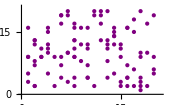

```mathematica
n=100;
data=Table[{RandomInteger[{1,20}],RandomInteger[{1,20}]},{n}];

ListPlot[
data,
PlotRange->{{0,21},{0,21}},
PlotStyle->Directive[Purple,PointSize[Medium]],
ImageSize->170
]
```

code 2.2 RandomReal

(*This code generates random data points for a smooth curve by adding random noise to the function Sin[x].The RandomReal function with the interval {-0.1,0.1} is used to generate random noise.The data variable is a list of x and y values generated using the Table function with a step size of 10/n.The data points are plotted using the ListPlot function with the PlotRange option set to All:*)

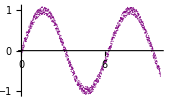

```mathematica
n=1000;
data=Table[{x,Sin[x]+RandomReal[{-0.1,0.1}]},{x,0,10,10/n}];

ListPlot[
data,
PlotRange->All,
PlotStyle->Purple,
ImageSize->170
]
```

code 2.3 RandomPoint

(* Generate a list of points in a unit disk: *)

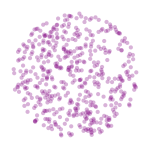

```mathematica
pts=RandomPoint[Disk[],500];

Graphics[
{PointSize[0.02],Purple,Opacity[0.3],Point[pts]},
ImageSize->150
]
```

code 2.4 RandomChoice

(*This code uses the RandomChoice function to generate 10000 rolls of two six-sided dice, sums the values of the dice, and stores the results in the variable rolls.It then creates a table counts of the number of times each possible sum occurs, from 2 to 12. Finally, it displays the frequency of each sum using a BarChart with labeled bars:*)

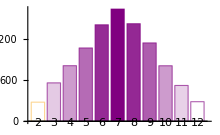

```mathematica
rolls=Table[
RandomChoice[Range[6]]+RandomChoice[Range[6]],
{10000}
];

counts=Table[
Count[rolls,i],{i,2,12}
];

BarChart[
counts,
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ChartLabels->Range[2,12],
ImageSize->220
]
```

code 2.5 RandomSample

(*This code plots the sine function f[x] between 0 and 2 Pi,and then superimposes 10 Purple points on the plot.These points are randomly sampled from a list of equidistant points on the function.The RandomSample function is called with the list of points as the first argument,and 10 as the second argument to select 10 random points from the list:*)

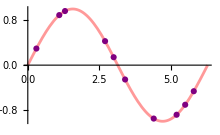

```mathematica
f[x_]:=Sin[x];
Plot[
f[x],{x,0,2π},
PlotStyle->{Red,Opacity[0.4]},
Epilog->{
PointSize[0.02],
Purple,
Point[
RandomSample[
Table[{x,f[x]},{x,0,2π,0.1}],
10]
]
},
ImageSize->220
]
```

code 2.6 RandomVariate

(*The code uses the Table function to generate a list of n random variables drawn from a normal distribution with mean mu and standard deviation sigma using the RandomVariate function.This list is then passed to ListPlot to create the plot.The Manipulate function allows for interactive exploration of the plot by adjusting the values of n,mu,and sigma.This code can be used as a starting point for more advanced statistical simulations and explorations.For example,one could modify the code to simulate data from a different distribution,or to add additional controls for exploring different aspects of the distribution (such as skewness or kurtosis):*)

```mathematica
Manipulate[
ListPlot[
Table[
RandomVariate[NormalDistribution[μ,σ]],
{n}
],
Filling->Axis,
PlotStyle->{Directive[Purple,Opacity[0.8]]},
PlotRange->{{0,100},{-10,10}},
ImageSize->300
],
{{n,50},1,100,1},
{{μ,0},-5,5,0.1},
{{σ,1},0.1,5,0.1}
]
```

Some of the most commonly used Mathematica functions include Histogram, and Histogram3D. By using these functions, you can gain a deeper understanding of the underlying patterns in your data and make informed decisions based on your findings.

Histogram[{x1,x2,…}]			plots a histogram of the values xi.

Histogram[{x1,x2,…},bspec]		plots a histogram with bin width specification bspec.

Histogram[{x1,x2,…},bspec,hspec]	plots a histogram with bin heights computed according to the specification hspec.

Histogram[{data1,data2,…},…]		plots histograms for multiple datasets datai.

Histogram3D[{{x1,y1},{x2,y2},…}]	plots a 3D histogram of the values {xi,yi}.

Histogram3D[{{x1,y1},{x2,y2},…},bspec]	plots a 3D histogram with bins specified by bspec.

Histogram3D[{{x1,y1},{x2,y2},…},bspec, hspec] plots a 3D histogram with bin heights computed according to the specification hspec.

Histogram3D[{data1,data2,…}]		plots 3D histograms for multiple datasets datai.

Remarks:

• The following bin specifications bpsec can be given:

n		use n bins

{dx}		use bins of width dx

{xmin,xmax,dx}	use bins of width dx from xmin to xmax

{{b1,b2,…}}	use bins [b1,b2),[b2,b3),…

Automatic	determine bin widths automatically

“name”		use a named binning method

{“Log”,bspec}	apply binning bspec on log-transformed data

fb		apply fb to get an explicit bin specification {b1,b2,…}

• Possible named binning methods include:

“Sturges”		compute the number of bins based on the length of data

“Scott”			asymptotically minimize the mean square error

“FreedmanDiaconis”	twice the interquartile range divided by the cube root of sample size

“Knuth”		balance likelihood and prior probability of a piecewise uniform model

“Wand”			one-level recursive approximate Wand binning

• Different forms of histogram can be obtained by giving different bin height specifications hspec in Histogram[data,bspec,hspec]. The following forms can be used:

“Count”		the number of values lying in each bin

“CumulativeCount”	cumulative counts

“SurvivalCount”	survival counts

“Probability”		fraction of values lying in each bin

“Intensity”		count divided by bin width

“PDF”			probability density function

“CDF”			cumulative distribution function

“SF”			survival function

“HF”			hazard function

“CHF”			cumulative hazard function

{“Log”,hspec}		log-transformed height specification

fh			heights obtained by applying fh to bins and counts

code 2.7 Histogram

(*This code generates six histograms of 500 random samples drawn from a normal distribution with mean 0 and standard deviation 1,using different methods to set the vertical scale of the histograms.The different methods used are:”Count”,”Probability”,”PDF”,”CumulativeCount”,”CDF”,and “SF”.This allows for a comparison of different ways of visualizing the same data,which can help in understanding the data and selecting the most appropriate method for a particular analysis:*)

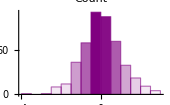
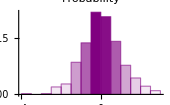
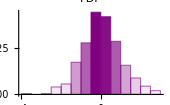
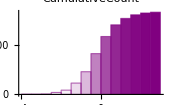
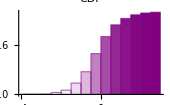
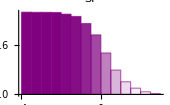

```mathematica
sampledata=RandomVariate[
NormalDistribution[0,1],
500
];

Table[
Histogram[
sampledata,
Automatic,
heightmethod,
PlotLabel->heightmethod,
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->170
],
{heightmethod,{"Count","Probability","PDF","CumulativeCount","CDF","SF"}}
]
```

code 2.8 Histogram

(*This code generates a histogram of 1000 random samples drawn from a normal distribution with mean 0 and standard deviation 1. The resulting histogram has no outline or borders around the bars and is colored in purple.Without the borders around the bars,the shape of the distribution may be more apparent.This can be especially useful when comparing multiple histograms with different data sets or parameters:*)

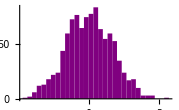

```mathematica
Histogram[
RandomVariate[
NormalDistribution[0,1],
1000
],
ChartBaseStyle->EdgeForm[None],
ChartStyle->Purple,
ImageSize->179
]
```

code 2.9 Histogram3D

(*This code generates a sequence of 3D histograms for a random sample of size 300 from a bivariate normal distribution with mean 0 and standard deviation 1 in each dimension.The use of different height functions allows for a more comprehensive understanding of the sample’s distribution and provides a range of useful visualization tools for data analysis:*)

```mathematica
sampledata=RandomVariate[
NormalDistribution[0,1],
{300,2}
];

Table[
Histogram3D[
sampledata,
Automatic,
height,
PlotLabel->height,
ColorFunction->Function[{height},Opacity[0.9]],
ChartStyle->RGBColor[0.6,0.30,0.60],
ImageSize->170
],
{height,{"Count","Probability","PDF","CDF","SF","HF"}}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

The Wolfram Language’s descriptive statistics functions operate both on explicit data and on symbolic representations of statistical distributions, making it a valuable tool for data analysis and exploratory data science tasks.

Mean[list]		gives the statistical mean of the elements in list.

Mean[dist]		gives the mean of the distribution dist.

Median[list]		gives the median of the elements in list.

Median[dist]		gives the median of the distribution dist.

Commonest[list]	gives a list of the elements that are the most common in list.

Commonest[list,n]	gives a list of the n most common elements in list.

TrimmedMean[list,f]	gives the mean of the elements in list after dropping a fraction f of the smallest and largest elements.

TrimmedMean[dist,…]	gives the trimmed mean of a univariate distribution dist.

WinsorizedMean[list,f]	gives the mean of the elements in list after replacing the fraction f of the smallest and largest elements by the remaining extreme values.

WinsorizedMean[dist,…] gives the winsorized mean of a univariate distribution dist.

HarmonicMean[list]	gives the harmonic mean of the values in list.

GeometricMean[list]	gives the geometric mean of the values in list.

RootMeanSquare[list]	gives the root mean square of values in list.

RootMeanSquare[dist]	gives the root mean square of the distribution dist.

Quartiles[list]		gives a list of the 1/4, 1/2 and 3/4 quantiles of the elements in list.

Quartiles[dist]		gives a list of the 1/4, 1/2 and 3/4 quantiles of the distribution dis

code 2.10 Mean

(*The code analyzes a dataset of heights by calculating the mean and generating two plots.The first plot displays the data set, while the second plot displays the data set along with horizontal line for the mean:*)

127.

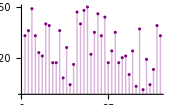

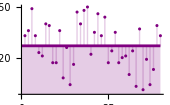

```mathematica
h={133,136,149,133,123,121,140,139,117,117,136,108,126,104,116,147,140,148,150,122,135,146,133,144,117,124,135,117,120,121,110,124,103,137,101,119,104,113,139,133};

m=N[Mean[h]]
n=Length[h];

ListPlot[
h,
Filling->Axis,
PlotStyle->Purple,
ImageSize->170
]

ListPlot[
{h,{{0,m},{n,m}}},
Joined->{False,True},
Filling->{1->m,2->Axis},
PlotStyle->Purple,
ImageSize->170,
PlotLegends->{None,"Mean =127"}
]
```

code 2.11 Commonest

(*The code reads in a dataset h of heights and calculates Commonest elements.It then produces two plots:a scatter plot of the dataset h,and a plot that shows both h and three horizontal lines at the commonest elements and mean.These plots are used for visualizing the distribution of the dataset and highlighting the location of the commonest elements and mean:*)

{{133,4},{136,2},{149,1},{123,1},{121,2},{140,2},{139,2},{117,4},{108,1},{126,1},{104,2},{116,1},{147,1},{148,1},{150,1},{122,1},{135,2},{146,1},{144,1},{124,2},{120,1},{110,1},{103,1},{137,1},{101,1},{119,1},{113,1}}

{101.,103.,104.,108.,110.,113.,116.,117.,119.,120.,121.,122.,123.,124.,126.,133.,135.,136.,137.,139.,140.,144.,146.,147.,148.,149.,150.}

127

-Graphics-

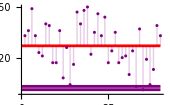

```mathematica
h={133,136,149,133,123,121,140,139,117,117,136,108,126,104,116,147,140,148,150,122,135,146,133,144,117,124,135,117,120,121,110,124,103,137,101,119,104,113,139,133};

Tally[h]
c=N[Complement[h]]
m=Mean[h]
n=Length[h];

ListPlot[
h,
Filling->Axis,
PlotStyle->Purple,
ImageSize->170
]

ListPlot[
{h,{{0,c[[1]]},{n,c[[1]]}},{{0,c[[2]]},{n,c[[2]]}},{{0,m},{n,m}}},
Joined->{False,True,True,True},
Filling->{1->m,2->{3}},
PlotStyle->{Purple,Purple,Purple,Red},
ImageSize->170,
PlotLegends->{"h","Commonest=133","Commonest=117","Mean =127"}
]
```

code 2.12 HarmonicMean, GeometricMean and Mean

(*The code will generate a list of random numbers,calculate their Harmonic Mean,Geometric Mean,and Arithmetic Mean,and then plot the means against the number of elements in the list.For positive data,we can see that Harmonic Mean<=Geometric Mean<=Arithmetic Mean:*)

{4.05091,4.96548,5.76365}

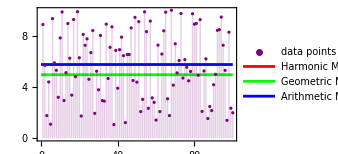

```mathematica
SeedRandom[1234];
n=100;
d=RandomReal[{1,10},n];
hm=HarmonicMean[d];
gm=GeometricMean[d];
am=Mean[d];
means={hm,gm,am}
labels={"data points","Harmonic Mean","Geometric Mean","Arithmetic Mean"};

plot=ListPlot[
{d,{{0,hm},{h,hm}},{{0,gm},{n,gm}},{{0,am},{n,am}}},
Joined->{False,True,True,True},
Filling->{1->Axis},
Frame->True,
PlotRange->All,
PlotStyle->{Purple,Red,Green,Blue},
PlotLegends->labels,
ImageSize->250
]
```

The Mathematica function BoxWhiskerChart is a powerful tool for visualizing and analyzing data distributions. Here are some features of this function:

• Clear representation of data: BoxWhiskerChart provides a clear and concise representation of the distribution of a dataset. It displays important statistical measures such as the median, quartiles, and outliers, making it easy to understand the central tendency and spread of the data.

• Customizable appearance: The function offers a wide range of options to customize the appearance of the box-and-whisker plot. You can adjust the colors, styles, and sizes of the boxes, whiskers, outliers, and other elements to suit your preferences or match your presentation or publication style.

• Comparative analysis: BoxWhiskerChart allows for easy comparison of multiple datasets. You can plot several box-and-whisker diagrams side by side or in a stacked manner, making it straightforward to identify differences or similarities in distributions.

• Interaction and exploration: The resulting chart is interactive, meaning you can hover over different elements to obtain more detailed information about specific data points or summary statistics. This interactivity enhances the exploratory data analysis process and allows for a deeper understanding of the underlying distribution.

BoxWhiskerChart[{x1,x2,…}]		makes a box-and-whisker chart for the values xi.

BoxWhiskerChart[{x1,x2,…},bwspec]	makes a chart with box-and-whisker symbol specification bwspec.

BoxWhiskerChart[{data1,data2,…},…]	makes a chart with box-and-whisker symbol for each datai.

BoxWhiskerChart[{{data1,data2,…},…},…]makes a box-and-whisker chart from multiple groups of datasets {data1,data2,…}.

BoxWhiskerChart draws a box-and-whisker summary of the distribution of values in each datai. See the following figure

-Graphics-

The following box-and-whisker specifications bwspec can be given:

“Notched”			median confidence interval notch

“Outliers”			outlier markers

“Median”			median marker

“Basic”				box-and-whisker only

“Mean”				mean marker

“Diamond”			mean confidence interval diamond

{{elem1,val11,…},…}		box-and-whisker element specification

{“name”,{elem1,val11,…},…}	named bwspec with element modifica

code 2.13 BoxWhiskerChart

(*The code uses the RandomVariate function to generate a data vector with 200 values.It samples from a normal distribution with a mean of 1 and a standard deviation of 2. then,the code generates a basic box-and-whisker chart using randomly generated data:*)

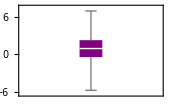

```mathematica
BoxWhiskerChart[
RandomVariate[
NormalDistribution[1,2],
200
],
ChartStyle->Purple,
ImageSize->170
]
```

code 2.14 BoxWhiskChart

(*The code demonstrates customization options for a box-and-whisker chart.It generates a list of seven datasets,each containing 200 data points randomly sampled from normal distributions.The mean of each dataset is randomly chosen from the integers 0 to 6,while the standard deviation is fixed at 1. The first BoxWhiskerChart call creates a notched box-and-whisker chart,displaying confidence intervals around the medians of each dataset.The second BoxWhiskerChart call explicitly shows outliers,highlighting extreme or unusual data points:*)

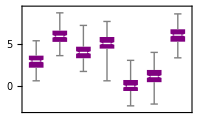

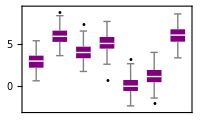

```mathematica
data=Table[
RandomVariate[
NormalDistribution[RandomInteger[6],1],
200
],
{7}
];

BoxWhiskerChart[
data,
"Notched",
ChartStyle->Purple,
ImageSize->200
]

BoxWhiskerChart[
data,
"Outliers",
ChartStyle->Purple,
ImageSize->200
]
```

code 2.15 BoxWhiskerChart

(*The code generates a series of BoxWhiskerCharts to visualize the distribution of a dataset called’data’ using the SkewNormalDistribution.The dataset has dimensions 8 rows by 200 columns.The code uses the BoxWhiskerChart function to create a box and whisker plot for each column in the’data’ dataset.Each chart represents statistical measures such as the minimum,mean,median,and maximum values with different line styles and colors:*)

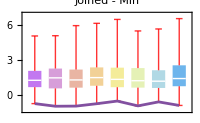
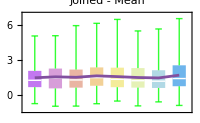
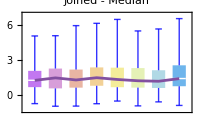
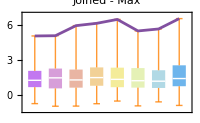

```mathematica
data=RandomVariate[
SkewNormalDistribution[0,2,4],
{8,200}
];

Table[
BoxWhiskerChart[
data,
{
{"Whiskers",Directive[Thick,s[[2]],Opacity[0.8]]},
{"Fences",Directive[Thick,s[[2]],Opacity[0.8]]}
},
Joined->s[[1]],
PlotLabel->Style[Row[{"Joined - ",s[[1]]}]],
ChartStyle->"Pastel",
ImageSize->200
],
{s,{{"Min",Red},{"Mean",Green},{"Median",Blue},{"Max",Orange}}}
]
```

code 2.16 BoxWhiskerChart

(*The code generates multiple density plots using the DistributionChart function.It generates a 2D array of random data called data.It consists of 10 rows and 100 columns,where each element is sampled from a standard normal distribution.The code then uses a combination of Table and DistributionChart to generate density plots for each element in the list of chart element functions.The Joined option is set to “Mean” to connect the mean values of the distributions with a line.The ChartElementFunction option is used to specify different chart element functions,such as “PointDensity” and “LineDensity”.*)

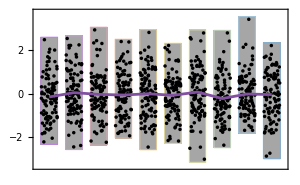
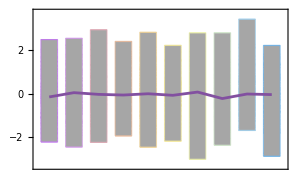

```mathematica
data=RandomVariate[NormalDistribution[],{10,100}];

Table[
DistributionChart[
data,
Joined->"Mean",
ChartElementFunction->s,
ChartStyle->"Pastel",
ImageSize->300
],
{s,{"PointDensity","LineDensity"}}
]
```

code 2.17 BoxWhiskerChart

(*The code generates three sets of random data (data1,data2,data3) by sampling from a normal distribution with different means (μ) using RandomVariate.Each set consists of 500 data points.The BoxWhiskerChart function is used to create a box-and-whisker plot.The Epilog option is used to add additional elements to the chart.In this code,points are overlaid on the chart to represent the individual data points of each dataset.The points are created using Map and Transpose.The random displacement in the x-axis is in a range of-0.25 to 0.25:*)

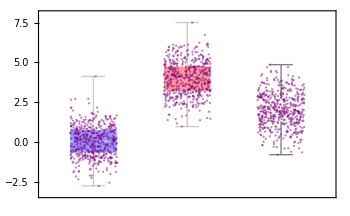

```mathematica
{data1,data2,data3}=Table[
RandomVariate[NormalDistribution[μ,1],500],
{μ,{0,4,2}}
];
BoxWhiskerChart[
{data1,data2,data3},
ChartStyle->{Directive[Blue,Opacity[0.4]],Directive[Red,Opacity[0.4]],Directive[White,EdgeForm[Thickness[0.001]]]},
ImageSize->350,
Epilog->{
Directive[Purple,Opacity[0.5]],
PointSize[0.0045],
Map[
Point,{
Transpose[{ConstantArray[1,Length[data1]]+RandomReal[{-0.25,0.25},Length[data1]],data1}],
Transpose[{ConstantArray[2,Length[data2]]+RandomReal[{-0.25,0.25},Length[data2]],data2}],
Transpose[{ConstantArray[3,Length[data3]]+RandomReal[{-0.25,0.25},Length[data3]],data3}]}
]
}
]
```

Dispersion statistics summarize the scatter or spread of the data. Most of these functions describe deviation from a particular location. For instance, variance is a measure of deviation from the mean. Mathematica provides a set of functions and tools for calculating, visualizing, and analyzing dispersion statistics, allowing users to gain deeper insights into the variability and distribution of their data. Let us go through them in detail.

InterquartileRange[list]		gives the difference between the upper and lower quartiles for the elements in list.

InterquartileRange[dist]	gives the difference between the upper and lower quartiles for the distribution dist.

QuartileDeviation[list]		gives the quartile deviation or semi-interquartile range of the elements in list.

QuartileDeviation[dist]		gives the quartile deviation or semi-interquartile range of the distribution dist.

MeanDeviation[list]		gives the mean absolute deviation from the mean of the elements in list.

StandardDeviation[list]		gives the sample standard deviation of the elements in list.

StandardDeviation[dist]	gives the standard deviation of the distribution dist.

Variance[list]			gives the sample variance of the elements in list.

Variance[dist]			gives the variance of the distribution dist.

TrimmedVariance[list,f]		gives the variance of the elements in list after dropping a fraction f of the smallest and largest elements.

TrimmedVariance[dist,…]	gives the trimmed variance of a univariate distribution dist.

WinsorizedVariance[list,f]	gives the variance of the elements in list after replacing the fraction f of the smallest and largest elements by the remaining extreme values.

WinsorizedVariance[dist,…]	gives the winsorized variance of a univariate distribution dist.

code 2.18 QuartileDeviation and StandardDeviation

(*This code generates a 2D dataset from a standard normal distribution and calculates various statistical measures such as quartile deviation,standard deviation,and mean for each component of the dataset.It then displays the results and creates a scatter plot with highlighted points representing the statistical measures:*)

Mean= {-0.0471428,0.00769483},
QuartileDeviation= {0.688361,0.685293},
 StandardDeviation={1.01234,1.02132}

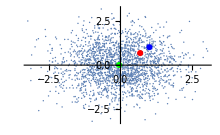

```mathematica
data=RandomVariate[
NormalDistribution[0,1],
{2000,2}
];

qdx=QuartileDeviation[data[[All,1]]];
qdy=QuartileDeviation[data[[All,2]]];

sdx=StandardDeviation[data[[All,1]]];
sdy=StandardDeviation[data[[All,2]]];

mx=Mean[data[[All,1]]];
my=Mean[data[[All,2]]];
Print[
"Mean= {",mx,",",my,"},\n",
"QuartileDeviation= {",qdx,",",qdy,"},\n ",
"StandardDeviation={",sdx,",",sdy,"} "
]

ListPlot[
data,
Epilog->{
Red,PointSize[0.02],Point[{qdx,qdy}],
Blue,PointSize[0.02],Point[{sdx,sdy}],
Green,PointSize[0.02],Point[{mx,my}]
},
ImageSize->220
]
```

code 2.19 StandardDeviation

(*The code generates a list of 1000 random numbers from a standard normal distribution.It then calculates the standard deviation of the data and creates a histogram plot with the probability density function (PDF).The plot includes red points representing the mean and±standard deviation of the data:*)

1.00031

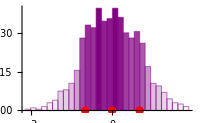

```mathematica
data=RandomVariate[
NormalDistribution[0,1],
1000
];

StandardDeviation[data]

Histogram[
data,
Automatic,
"PDF",
Epilog->{
Red,
PointSize[0.03],
Point[{{StandardDeviation[data],0},{Mean[data],0},{-StandardDeviation[data],0}}]
},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->200
]
```

code 2.20 Variance

```mathematica
Variance[{3.2,1.21,3.4,2,4.66,1.5,5.61,7.22}]
```

4.45003

```mathematica
Variance[{{4,1},{5.2,7},{5.3,8},{5.4,9}}]
Variance[{4,5.2,5.3,5.4}]
Variance[{1,7,8,9}]
```

{0.429167,155/12}

0.429167

155/12

```mathematica
data={8,3,5,4,9,0,4,2,2,3}; w={0.15,0.09,0.12,0.10,0.16,0.,0.11,0.08,0.08,0.09}; Variance[WeightedData[data,w]]
```

7.26594

(*This code creates a Manipulate function with slider and a dropdown menu.The n slider allows the user to adjust the sample size,while the dist dropdown menu allows the user to choose the distribution that the sample is drawn from.The code then uses RandomVariate to generate a sample of size n from the selected distribution,calculates the variance using Variance,and displays both a ListPlot and a Histogram of the sample data along with the calculated variance.*)

```mathematica
Manipulate[
Module[
{data,var},
data=RandomVariate[dist,n];
var=Variance[data];

Grid[
{
{
ListPlot[
data,
PlotRange->All,
ImageSize->250,
Filling->Axis,
PlotStyle->Purple
],
Histogram[
data,
"FreedmanDiaconis",
"PDF",
Frame->True,
FrameLabel->{"Data","PDF"},
ImageSize->250,
ColorFunction->Function[Opacity[0.7]],
ChartStyle->Purple
]
},
{Null,Text["Variance: "<>ToString[var]]}
}
]
],
{{n,300,"Sample size"},10,1000,10,Appearance->"Labeled"},{{dist,NormalDistribution[0,1],"Distribution"},{NormalDistribution[0,1],StudentTDistribution[3],ExponentialDistribution[1],UniformDistribution[{-1,1}]}},Alignment->Center
]
```

A variety of moments are used to summarize a distribution or data. Mean is used to indicate a center location, variance and standard deviation are used to indicate dispersion, etc. The Wolfram Language fully supports moments of any order, univariate or multivariate, for symbolic distributions and data. Moreover, you can get some information about the shape of a distribution using shape statistics functions. Skewness describes the amount of asymmetry. Kurtosis measures the concentration of data around the peak and in the tails versus the concentration in the flanks. let us start by considering moment functions.

Moment[list,r]		gives the r^(th) sample moment of the elements in list.

Moment[dist,r]		gives the r^(th) moment of the distribution dist.

CentralMoment[list,r]	gives the r^(th) central moment of the elements in list with respect to their mean.

CentralMoment[dist,r]	gives the r^(th) central moment of the distribution dist.

Skewness[list]		gives the coefficient of skewness for the elements in list.

Skewness[dist]		gives the coefficient of skewness for the distribution dist.

QuartileSkewness[list]	gives the coefficient of quartile skewness for the elements in list.

QuartileSkewness[dist]	gives the coefficient of quartile skewness for the distribution dist.

Kurtosis[list]		gives the coefficient of kurtosis for the elements in list.

Kurtosis[dist]		gives the coefficient of kurtosis for the distribution dist.

code 2.21 Moment and Kurtosis

```mathematica
list={1,2,3,4,5};
moment1=Mean[list]
Moment[list,1]
```

3

3

```mathematica
Moment[{x,y,z},2]
```

1/3 (x^2+y^2+z^2)

```mathematica
Kurtosis[{a,b,c}]
```

(3 ((a+1/3 (-a-b-c))^4+(b+1/3 (-a-b-c))^4+(1/3 (-a-b-c)+c)^4))/(((a+1/3 (-a-b-c))^2+(b+1/3 (-a-b-c))^2+(1/3 (-a-b-c)+c)^2)^2)

code 2.22 CentralMoment

(*In this code,the Manipulate function creates an interactive interface that allows you to explore the effects of changing the distributions and the order of the central moment.The code includes a histogram plot of the sample data using the Histogram function.The plot is displayed as a probability density function,and the calculated central moment is shown as a text label.The Manipulate parameters include the choice of distribution,sample size,and order of the central moment.The user can select different distributions,adjust the sample size using a slider,and modify the order of the central moment:*)

```mathematica
Manipulate[
Module[
{data,mean,centralMoment},
data=RandomVariate[Distribution,sampleSize];
centralMoment=CentralMoment[data,n];

Histogram[
data,
Automatic,
"PDF",
PlotRange->All,
PlotLabel->{Text["Central Moment ("<>ToString[n]<>"):"<>ToString[CentralMoment]]},
ImageSize->300,
ColorFunction->Function[Opacity[0.5]],
ChartStyle->Purple
]
],
{{Distribution,NormalDistribution[0,1],"Distribution:"},{NormalDistribution[0,1]->"Normal",GammaDistribution[2,1]->"Gamma",UniformDistribution[{-1,1}]->"Uniform"}},{{sampleSize,1000,"Sample Size:"},{100,500,1000,5000}},{{n,2,"Order of Central Moment:"},{1,2,3,4}}
]
```

code 2.23 Skewness

(*The code creates three skew normal distributions with different shape parameter α and visualizes their probability density functions (PDFs) on a plot.It computes the skewness values for each distribution and displays them in the plot legend.The code demonstrates how the shape parameter α affects the shape of the distributions:*)

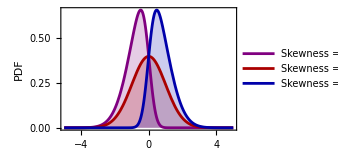

```mathematica
dist1=SkewNormalDistribution[0,1,-3];
dist2=SkewNormalDistribution[0,1,0];
dist3=SkewNormalDistribution[0,1,3];

skewness1=N[Skewness[dist1]];
skewness2=N[Skewness[dist2]];
skewness3=N[Skewness[dist3]];

Plot[
{PDF[dist1,x],PDF[dist2,x],PDF[dist3,x]},
{x,-5,5},
PlotStyle->{Purple,Darker[Red],Darker[Blue]},
Filling->Axis,
PlotLegends->{
"Skewness = "<>ToString[skewness1],
"Skewness = "<>ToString[skewness2],
"Skewness = "<>ToString[skewness3]
},
Frame->True,
FrameLabel->{"x","PDF"},
PlotRange->All,
ImageSize->250
]
```

### Probability Distributions

PDF[dist,x]	gives the probability density function for the distribution dist evaluated at x.

CDF[dist,x]	gives the cumulative distribution function for the distribution dist evaluated at x.

MomentGeneratingFunction[dist,t]	gives the moment-generating function for the distribution dist as a function of the variable t.

code 2.24 PDF, CDF and MomentGeneratingFunction

```mathematica
PDF[NormalDistribution[μ,σ],x]
CDF[NormalDistribution[μ,σ],x]
MomentGeneratingFunction[NormalDistribution[μ,σ],x]
Mean[NormalDistribution[μ,σ]]
Variance[NormalDistribution[μ,σ]]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

1/2 Erfc[(-x+μ)/(√2 σ)]

ⅇ^(x μ+(x^2 σ^2)/2)

μ

σ^2

code 2.25 PDF

(*The resulting 3D plot visualizes the PMF of the Multivariate Poisson distribution with specific parameter values n=1,a=2,and b=3. The plot allows you to observe the PMF values for different combinations of x and y within the specified ranges.Each cell in the plot represents the PMF value for a specific x and y combination:*)

```mathematica
pdf1=PDF[MultivariatePoissonDistribution[n,{a,b}],{x,y}]
pdf=PDF[MultivariatePoissonDistribution[1,{2,3}],{x,y}]

DiscretePlot3D[
pdf,
{x,0,10},
{y,0,10},
ExtentSize->0.6,
PlotStyle->Purple,
ImageSize->200
]

DiscretePlot3D[
pdf,
{x,0,10},
{y,0,10},
PlotRange->All,
PlotStyle->Purple,
ImageSize->200
]
```

Piecewise[{{(b^(-x+y) ⅇ^(-a-b-n) (-n)^x HypergeometricU[-x,1-x+y,-(a b)/n])/(x! y!), x≥0&&y≥0}, {0, True}}]

Piecewise[{{((-1)^x 3^(-x+y) HypergeometricU[-x,1-x+y,-6])/(ⅇ^6 x! y!), x≥0&&y≥0}, {0, True}}]

-Graphics3D-

-Graphics3D-

code 2.26 CDF

```mathematica
DiscretePlot3D[
CDF[MultivariatePoissonDistribution[5,{2,3}],{x,y}],
{x,0,12},
{y,0,12},
ExtentSize->Right,
PlotStyle->Lighter[Purple,0.1],
ImageSize->200
]
```

-Graphics3D-

BinomialDistribution[n,p]	represents a binomial distribution with n trials and success probability p.

DiscreteUniformDistribution[{imin,imax}] represents a discrete uniform distribution over the integers from imin to imax.

DiscreteUniformDistribution[{{im in,imax},{jmin,jmax},…}] represents a multivariate discrete uniform distribution over integers within the box {{imin,imax},{jmin,jmax},…}.

NormalDistribution[μ,σ]	represents a normal (Gaussian) distribution with mean μ and standard deviation σ.

NormalDistribution[]		represents a normal distribution with zero mean and unit standard deviation.

UniformDistribution[{min,max}]represents a continuous uniform statistical distribution giving values between min and max.

UniformDistribution[]		represents a uniform distribution giving values between 0 and 1.

EstimatedDistribution[data,dist]estimates the parametric distribution dist from data.

code 2.27 BinomialDistribution

(*The code generates a discrete plot of the PMF for a binomial distribution with parameters n=30 and three different values of p (0.2,0.5,and 0.7).The plot shows the values of the PMF for all possible values of k between 0 and 37:*)

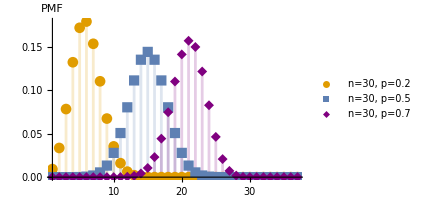

```mathematica
DiscretePlot[
Evaluate[
Table[
PDF[
BinomialDistribution[30,p],k
],
{p,{0.2,0.5,0.7}}
]
],
{k,37},
PlotRange->All,
PlotMarkers->Automatic,
PlotLegends->Placed[{"n=30, p=0.2","n=30, p=0.5","n=30, p=0.7"},{0.8,0.75}],
PlotStyle->{RGBColor[0.88,0.61,-.14],RGBColor[0.37,0.5,0.7],Purple},
ImageSize->320,
AxesLabel->{None,"PMF"}
]
```

code 2.28 DiscreteUniformDistribution

(*The code generates a discrete plot of the PMF for a discrete uniform distribution with parameters a=1 and three different values of b (8,12,and 16).The plot shows the values of the PMF for all possible values of j between 0 and 26:*)

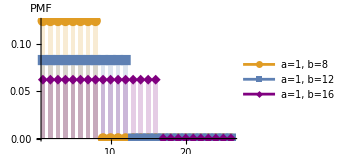

```mathematica
DiscretePlot[
Evaluate[
Table[
PDF[
DiscreteUniformDistribution[{1,b}],j
],
{b,{8,12,16}}
]
],
{j,26},
ExtentSize->1/2,
PlotRange->All,
PlotMarkers->Automatic,
PlotLegends->Placed[{"a=1, b=8","a=1, b=12","a=1, b=16"},{0.8,0.75}],
PlotStyle->{RGBColor[0.88,0.61,0.14],RGBColor[0.37,0.5,0.7],Purple},
ImageSize->250,
AxesLabel->{None,"PMF"}
]
```

code 2.29 UniformDistribution

(*The code creates a dynamic histogram of data and a plot of the PDF generated from Uniform distribution using the Manipulate function.The Manipulate function creates interactive controls for the user to adjust the values of min and max,which are the parameters of the Uniform distribution and the sample size:*)

```mathematica
Manipulate[
Module[
{
data=RandomVariate[
UniformDistribution[{min,max}],n
]
},

Show[
Histogram[
data,
Automatic,
"PDF",
ColorFunction->Function[{height},Opacity[height]],
ImageSize->320,
ChartStyle->Purple
],
Plot[
PDF[
UniformDistribution[{min,max}],x
],
{x,0,7},
ColorFunction->"Rainbow"
]
]
],
{{min,1,"min"},1,4,0.1},
{{max,4.5,"max"},4.5,7,0.1},
{{n,300,"n"},100,1000,10}
]
```

code 2.30 UniformDistribution

(*The code generates a 2D dataset with 1000 random points that follow Uniform distribution with min=0 and max=6. The dataset is then used to create a row of three plots.The first plot is a histogram of the X-axis values of the dataset.The second plot is a histogram of the Y-axis values of the dataset.It is similar to the first plot,but shows the distribution of the Y-axis values instead.The third plot is a scatter plot of the dataset,with the X-axis values on the horizontal axis and the Y-axis values on the vertical axis.Each point in the plot represents a pair of X and Y values from the dataset:*)

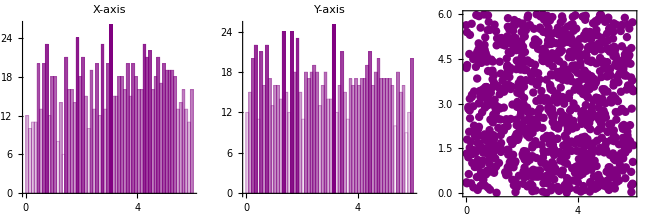

```mathematica
data=RandomVariate[
UniformDistribution[{0,6}],
{1000,2}
];

GraphicsRow[
{
Histogram[
data[[All,1]],
{0.1},
PlotLabel->"X-axis",
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple
],
Histogram[
data[[All,2]],
{0.1},
PlotLabel->"Y-axis",
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple
],
ListPlot[
data,
PlotStyle->{Purple,PointSize[0.015]},
AspectRatio->1,
Frame->True,
Axes->False
]
}
]
```

code 2.31 NormalDistribution

(*The code generates a plot of the probability density function (PDF) for a normal distribution with different values of standard deviation σ=(0.75,1 and 2) and a fixed mean (μ=0).The plot shows the values of the PDF for all possible values of x between-7 and 7. The resulting plot shows the bell-shaped curve of the normal distribution with different shapes,reflecting the impact of varying the value of the standard deviation:*)

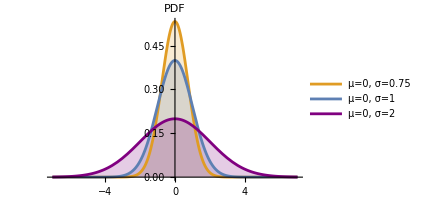

```mathematica
Plot[
Evaluate[
Table[
PDF[
NormalDistribution[0,σ],
x
],
{σ,{.75,1,2}}
]
],
{x,-7,7},
PlotRange->All,
Filling->Axis,
PlotLegends->Placed[{"μ=0, σ=0.75","μ=0, σ=1","μ=0, σ=2"},{0.8,0.75}],
PlotStyle->{RGBColor[0.88,0.61,0.14],RGBColor[0.37,0.5,0.7],Purple},
ImageSize->320,
AxesLabel->{None,"PDF"}
]
```

code 2.32 NormalDistribution

(*The code generates a histogram and a plot of the PDF for a Normal Distribution with parameters μ=1 and σ=3 and sample size 10000:*)

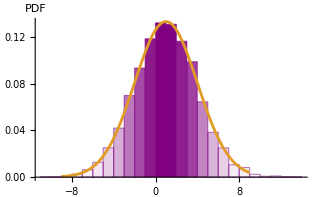

```mathematica
data=RandomVariate[
NormalDistribution[1,3],10^4
];

Show[
Histogram[
data,
20,
"PDF",
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->320,
AxesLabel->{None,"PDF"}
],
Plot[
PDF[
NormalDistribution[1,3],
x
],
{x,-9,9},
PlotStyle->RGBColor[0.88,0.61,0.14],
PlotRange->{0,4}
]
]
```

code 2.33 NormalDistribution

(*The code generates a set of random data points with a normal distribution in three dimensions,and then creates three histograms,one for each dimension,showing the distribution of the points along that axis.Additionally,it creates a 3D scatter plot of the data points:*)

```mathematica
data=RandomVariate[
NormalDistribution[0,1],
{1000,3}
];

GraphicsGrid[
{
{
Histogram[
data[[All,1]],
Automatic,
"PDF",
PlotLabel->"X-axis",
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple
],
Histogram[
data[[All,2]],
Automatic,
"PDF",
PlotLabel->"Y-axis",
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple
],
Histogram[
data[[All,3]],
Automatic,
"PDF",
PlotLabel->"Z-axis",
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple
],
ListPointPlot3D[
data,
BoxRatios->{1, 1, 1},
PlotStyle->{Purple,PointSize[0.015]}
]
}
}
]
```

-Graphics-

code 2.34 NormalDistribution

(*The code creates a Manipulate interface where the user can adjust the parameters of two normal distributions (dist1 and dist2) and see the resulting sum of these distributions (distSum) plotted on the same graph.The plot shows the PDFs of each distribution as well as the PDF of the sum of the distributions.The TransformedDistribution function is used to create the sum of two distributions by defining the distribution of the sum of two random variables,x and y,where x follows dist1 and y follows dist2.Hence,we prove that Normal distribution is closed under addition:*)

```mathematica
Manipulate[
dist1=NormalDistribution[mean1,sd1];
dist2=NormalDistribution[mean2,sd2];

distSum=TransformedDistribution[
x+y,
{Distributed[x,dist1],Distributed[y,dist2]}
];

Plot[
{
PDF[dist1,x],
PDF[dist2,x],
PDF[distSum,x]
},
{x,-5,5},
PlotRange->All,
AxesLabel->{"x","f(x)"},
Filling->{1->{2},2->{3}},
FillingStyle->{LightBlue,LightPurple},
PlotLegends->{"Distribution 1","Distribution 2","Sum of Distribution"}
],
{{mean1,0,"Mean 1"},-5,5,Appearance->"Labeled"},
{{sd1,1,"Standard Deviation 1"},0.1,5,Appearance->"Labeled"},
{{mean2,0,"Mean 2"},-5,5,Appearance->"Labeled"},
{{sd2,1,"Standard Deviation 2"},0.1,5,Appearance->"Labeled"}
]
```

code 2.35 NormalDistribution

(*The code generates a 3D scatter plot of normally distributed points,where the x-axis is red,y-axis is green,and z-axis is blue:*)

```mathematica
data=RandomVariate[
NormalDistribution[0,1],
{2000,3}
];

Graphics3D[
{
{PointSize[0.006],Purple,Point[data]},
Thin,
{Red,Opacity[0.4],Line[{{#,0,0},{#,0,-0.5}}]&/@data[[All,1]]},
Thin,
{Green,Opacity[0.4],Line[{{0,#,0},{0,#,-0.5}}]&/@data[[All,2]]},
Thin,
{Blue,Opacity[0.4],Line[{{0,0,#},{0,-0.5,#}}]&/@data[[All,3]]}
},
BoxRatios->{1, 1, 1},
Axes->True,
AxesLabel->{"X","Y","Z"},
ImageSize->320
]
```

-Graphics3D-

code 2.36 NormalDistribution and EstimatedDistribution

(* The code demonstrates a common technique in statistics and data analysis,which is the use of random sampling to estimate population parameters.The code generates random samples from a normal distribution with mean 0 and standard deviation 1,and then using these samples to estimate the parameters of another normal distribution with unknown mean and standard deviation.This process is repeated 20 times, resulting in 20 different estimated distributions.The code also visualizes the resulting estimated distributions using the PDF function.The code plots the PDFs of these estimated distributions using the PDF function and the estimated parameters.The plot shows the PDFs in a range from-3.5 to 3.5.The code also generates a list plot of 2 sets of random samples from the normal distribution with mean 0 and standard deviation 1. The plot shows the 100 random points generated from two random samples.The code generates also a histogram of the PDF for Normal distribution of the two samples: *)

{NormalDistribution[0.0450062,1.0891],NormalDistribution[-0.0169574,0.959468],NormalDistribution[0.0240091,1.01058],NormalDistribution[-0.0921747,1.03558],NormalDistribution[-0.0700857,0.986985],NormalDistribution[-0.0821871,0.918332],NormalDistribution[-0.0545345,1.00134],NormalDistribution[-0.1334,0.991557],NormalDistribution[0.135625,1.07366],NormalDistribution[0.078946,1.0904],NormalDistribution[-0.0789097,0.90149],NormalDistribution[0.0297704,0.990882],NormalDistribution[0.094619,0.992864],NormalDistribution[0.0269679,1.07632],NormalDistribution[-0.0854802,1.04702],NormalDistribution[0.0555461,0.951296],NormalDistribution[0.0585938,0.96048],NormalDistribution[0.152394,1.05118],NormalDistribution[-0.0169717,0.998316],NormalDistribution[0.125773,0.900428]}

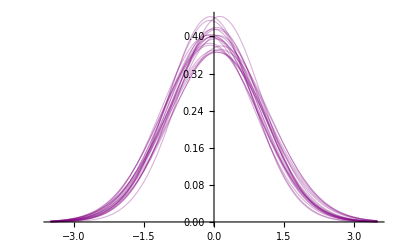

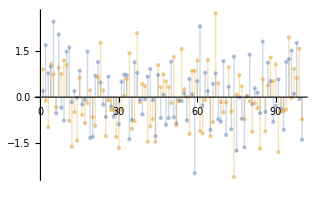

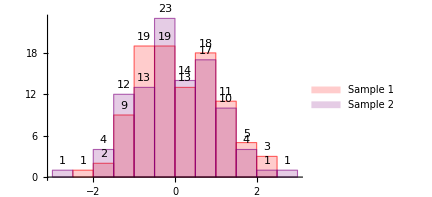

```mathematica
estim0distributions=Table[
dist=NormalDistribution[0,1];

sampledata=RandomVariate[
dist,
100
];

ed=EstimatedDistribution[
sampledata,
NormalDistribution[α,β]
],
{i,1,20}
]

pdf0ed=Table[
PDF[estim0distributions[[i]],x],
{i,1,20}
];

Plot[
pdf0ed,
{x,-3.5,3.5},
PlotRange->Full,
ImageSize->400,
PlotStyle->Directive[Purple,Opacity[0.3],Thickness[0.002]]
]

table=Table[
dist=NormalDistribution[0,1];
sampledata=RandomVariate[
dist,
100],
{i,1,2}
];

ListPlot[
table,
ImageSize->320,
Filling->Axis,
PlotStyle->Directive[Opacity[0.5],Thickness[0.003]]
]

Histogram[
table,
Automatic,
LabelingFunction->Above,
ChartLegends->{"Sample 1","Sample 2"},
ChartStyle->{Directive[Opacity[0.2],Red],Directive[Opacity[0.2],Purple]},
ImageSize->320
]
```